```mathematica
deploy
```

Wed 15 May 2019 10:13:57

Uploading to pytorch-fd/fluctuation-dissipation.nb

CloudObject[https://www.wolframcloud.com/objects/yaroslavvb/pytorch-fd/fluctuation-dissipation.nb]

## Util

```mathematica
(* utils *)
movingAvg[ys_,avg_]:=Module[{},
xs=Range@Length@ys;
Transpose@{MovingAverage[xs,avg],MovingAverage[ys,avg]}
]

(* column vectorize, following Magnus, 1999 *)
vec[W_]:=Transpose@{Flatten@Transpose[W]};
unvec[Wf_, rows_]:=Transpose[Flatten/@Partition[Wf,rows]];
toscalar[v_]:=Block[{t},
t=Flatten@v;
Assert[Length[t]==1, "scalar assert"];
First@t
];

v2c[c_]:=Transpose[{c}] (* turns vector to column matrix *)
v2r[c_]:={c} (* turns vector to row matrix *)
c2v[c_]:=Flatten[c] (* turns column matrix into vector *)

(* dot product that works on matrices *)
Unprotect[CircleDot];
DotProduct[a_,b_]:=Inner[Times,Flatten@a,Flatten@b,Plus];
CircleDot=DotProduct;

(* deploys with canonical name *)
deploy:=Module[{notebookFn, parentDir,cloudFn,result},
Print[DateString[]];
notebookFn=FileNameSplit[NotebookFileName[]][[-1]];
parentDir=FileNameSplit[NotebookFileName[]][[-2]];
cloudFn=parentDir~StringJoin~"/"~StringJoin~notebookFn;
result=CloudDeploy[SelectedNotebook[],CloudObject[cloudFn],Permissions->"Public",SourceLink->None];
Print["Uploading to ",cloudFn];
result
]


(* centers data where batch dimension is 1 *)
centerData[X_]:=Module[{Xc},
Xc=Mean@Transpose@X;
Transpose[#-Xc&/@Transpose[X]]
];

(* Generate 2D data for least-squares regression.
e ∈ [0,1): off-diagonal offset from singular covariance. 1 is unit normal, 0 is singular
dsize: number of datapoints


Returns: {X,Y} where X has shape 2,dsize, Y is 1,dsize *)
generateXY[e_,dsize_]:=Module[{n,wt,mean,cov,normal,X,Y},
n=2;  (* dimensions *) 
wt={{1,1}};(* true predictor weights *)
mean=0&/@Range@n;
cov={{1,1-e},{1-e,1}};
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
X=centerData[X];
Y=Dot[wt,X]+RandomVariate[NormalDistribution[0,1],{1,dsize}];
{X,Y}];

(* Generate multidimensional X data in n dimensions *)
generateX[n_,e_,dsize_]:=Module[{wt,mean,cov,normal,X},
mean=Table[0,{n}];
cov=IdentityMatrix[n]*e+Array[1-e&,{n,n}];
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose
(*centerData[X]*)
];
```

## Problem setup: Quadratic

Least squares fit of y=wx by using SGD on w with shape [1,2]

Globals : dsize, X, Y, w0, err, gradList, lossList, fullGradList, loss, gradients, Cmat

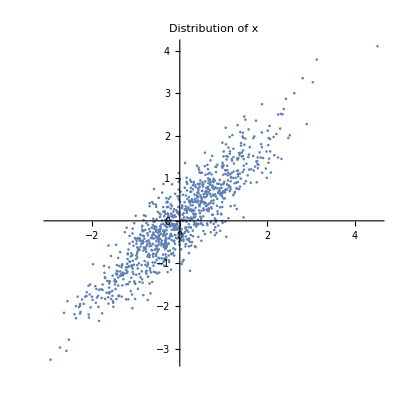

```mathematica
SeedRandom[0];
dsize=1000; (* number of datapoints *)
{X,Y}=generateXY[0.1,dsize];
err[w_]:=w.X-Y;   (* residuals, (1,dsize) *)
err[w_,i_]:={err[w][[All,i]]};   (* residuals, (1,dsize) *)
grad[w_]:=err[w].Xᵀ; (* full gradient *)
grad[w_,i_]:=
v2r[err[w][[1,i]]Transpose[X][[i,All]]]; (* gradient for 1 example *)
loss[w_]:=toscalar[err[w].err[w]ᵀ/2];
loss[w_,i_]:=toscalar[err[w,i].err[w,i]ᵀ/2];

(* Matrix of all gradients (dsize,2), i'th row is gradient for i'th example *)
gradients[w_]:=(DiagonalMatrix@Flatten@err[w]).Xᵀ;
(* Empirical Fisher matrix at current point estimated from the whole dataset *)
Cmat[w_]:=gradients[w]ᵀ.gradients[w]/dsize;
(* Empirical Fisher matrix at current point estimated from example i *)
Cmat[w_,i_]:=grad[w,i]ᵀ.grad[w,i];

maxIters=10000;
(* sequence of examples to sample *)
indices=RandomChoice[Range[dsize],maxIters];

optimizeSgd[lr_,w0_,iters_]:=Module[{g,w},
{pointList,gradList,fullGradList,lossList}={{},{},{},{}};
w=w0;
For[iter=1,iter≤iters,iter++,
g=grad[w,indices[[iter]]];
pointList=pointList~Append~w;
gradList=gradList~Append~g;
fullGradList=fullGradList~Append~grad[w];
lossList=lossList~Append~loss[w];
w=w-lr*g;
]
];

ListPlot[Transpose@X,AspectRatio->1,PlotLabel->"Distribution of x"]
```

## Non-stationary

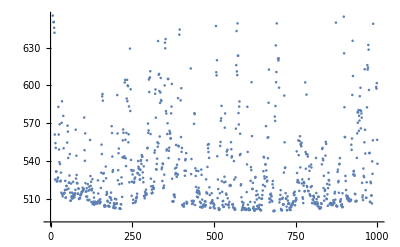

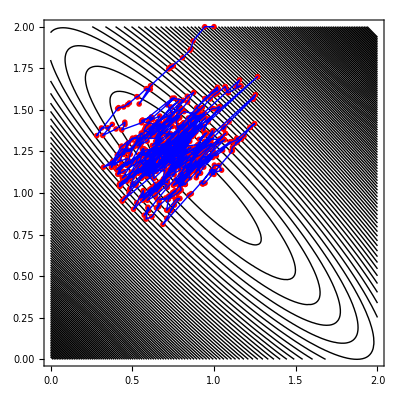

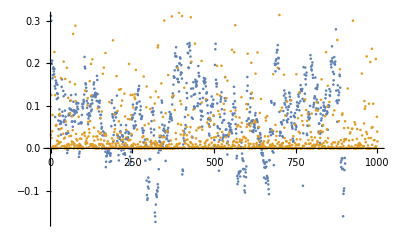

```mathematica
w0={{1,2}};
numSteps=1000;
η=0.05;
optimizeSgd[η,w0,numSteps]
ListPlot@lossList

bound=2;
plt1=ContourPlot[loss[{{x,y}}],{x,0,bound},{y,0,bound},Contours->100,ContourShading->None];
plotPoints=Flatten/@pointList;
plt3=Graphics[{Red,PointSize[0.01],Point[plotPoints]}];
plt4=Graphics[{Blue,Line[plotPoints]}];
Show[{plt1,plt3,plt4}]

(* Empirical Fisher matrix at current point estimated from example i *)
Cmat[w_,i_]:=grad[w,i]ᵀ.grad[w,i];

ol=MapThread[DotProduct,{gradList,pointList}];
or=MapThread[.5η Tr[Cmat[#1,#2]]&,{pointList,indices[[;;numSteps]]}];
ListPlot[{MovingAverage[ol,100],or}]
```

## Stationary

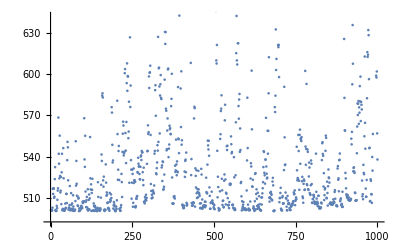

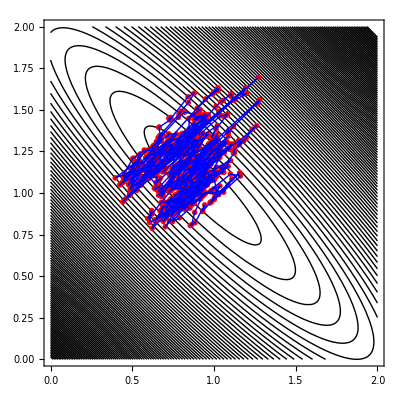

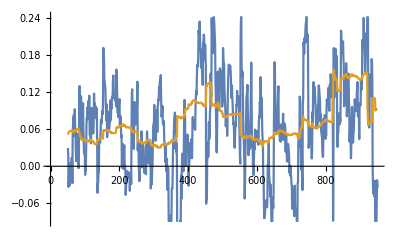

```mathematica
w0={{1,1}};

numSteps=1000;
η=0.05;
optimizeSgd[η,w0,numSteps]
ListPlot@lossList

bound=2;
plt1=ContourPlot[loss[{{x,y}}],{x,0,bound},{y,0,bound},Contours->100,ContourShading->None];
plotPoints=Flatten/@pointList;
plt3=Graphics[{Red,PointSize[0.01],Point[plotPoints]}];
plt4=Graphics[{Blue,Line[plotPoints]}];
Show[{plt1,plt3,plt4}]

(* Empirical Fisher matrix at current point estimated from example i *)
Cmat[w_,i_]:=grad[w,i]ᵀ.grad[w,i];

ol=MapThread[DotProduct,{gradList,pointList}];
or=MapThread[.5η Tr[Cmat[#1,#2]]&,{pointList,indices[[;;numSteps]]}];
ListLinePlot[{movingAvg[ol,100],movingAvg[or,100]}]
```

```mathematica
Mean[ol]/Mean[or]
```

0.894134

```mathematica
Variance[ol]/Variance[or]
```

61.3915

## Isotropic high-dimensional Case

```mathematica
dims=20;
wt={Array[1&,{dims}]};
w0=wt;
v2=0.01;
X=generateX[dims,1,dsize];
Y=Dot[wt,X]+RandomVariate[NormalDistribution[0,v2],{1,dsize}];
```

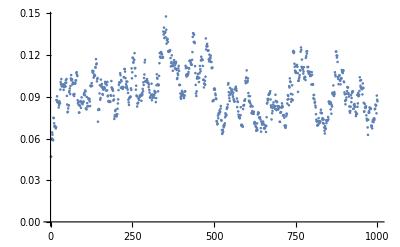

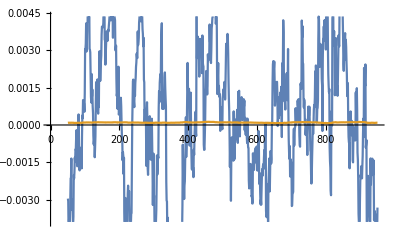

1.58495

```mathematica
numSteps=1000;
η=0.05;
optimizeSgd[η,w0,numSteps]
ListPlot@lossList
Cmat[w_,i_]:=grad[w,i]ᵀ.grad[w,i];
ol=MapThread[DotProduct,{gradList,pointList}];
or=MapThread[.5η Tr[Cmat[#1,#2]]&,{pointList,indices[[;;numSteps]]}];
ListLinePlot[{movingAvg[ol,100],movingAvg[or,100]}]
Mean[ol]/Mean[or]
```